```mathematica
Integrate[Exp[-x^2](x-t)^(r-1),{x,t,Infinity}]
```

If[Re[r]>0&&Re[t]>0,2^-r ⅇ^(-t^2) Gamma[r] HypergeometricU[r/2,1/2,t^2],Integrate[ⅇ^(-x^2) (-t+x)^(-1+r),{x,t,∞},Assumptions→Re[r]≤0||Re[t]≤0]]

```mathematica
Integrate[HypergeometricU[r/2,1/2,t^2],{t,xn,Infinity}]
```

If[Re[r]>1&&xn>0,(xn HypergeometricU[r/2,3/2,xn^2])/(-1+r),Integrate[HypergeometricU[r/2,1/2,t^2],{t,xn,∞},Assumptions→xn≤0||Re[r]≤1]]

```mathematica
Integrate[Exp[-x^2]x^k,{x,t,Infinity}]
```

If[t>0||t∉Reals,1/2 (Gamma[(1+k)/2]+t^(1+k) (t^2)^(1/2 (-1-k)) (-Gamma[(1+k)/2]+Gamma[(1+k)/2,t^2])),Integrate[ⅇ^(-x^2) x^k,{x,t,∞},Assumptions→t≤0]]

```mathematica
N[{(xn HypergeometricU[r/2,3/2,xn^2])/(-1+r)}/.{xn->3,r->4}]
```

{0.00938477}

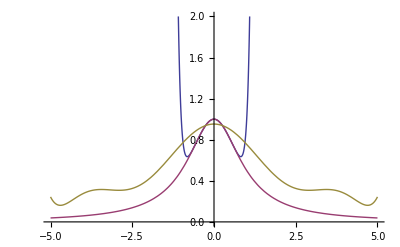

```mathematica
ss=Normal[Series[(1+x^2)^(-1),{x,0,12}]];
Plot[{ss,(1+x^2)^(-1),p},{x,-5,5},PlotRange->{{-5,5},{0,2}}]
```

```mathematica
Simplify[D[(1+x^2)^(-1),{x,10}]]
```

(3628800 (-1+55 x^2-330 x^4+462 x^6-165 x^8+11 x^10))/((1+x^2)^11)

```mathematica
NIntegrate[Exp[-x^2](1+x^2)^(-1),{x,-Infinity,Infinity}]
NIntegrate[Exp[-x^2]p,{x,-Infinity,Infinity}]
NIntegrate[Exp[-x^2]ss,{x,-Infinity,Infinity}]
```

1.34329

1.52191

246.066

```mathematica
p=1.965873223593163 10^-017 x^9+2.536350695103219 10^-005 x^8 -8.300073233634912 10^-016 x^7 -1.433272117147241 10^-003 x^6+1.068275583038658 10^-014 x^5 +2.781984033750018 10^-002 x^4-4.354156092558282 10^-014 x^3-2.243596684984556 10^-001 x^2 +3.479187673332162 10^-014 x^1+9.524823232181827 10^-001 x^0
```

0.952482+3.47919×10^-14 x-0.22436 x^2-4.35416×10^-14 x^3+0.0278198 x^4+1.06828×10^-14 x^5-0.00143327 x^6-8.30007×10^-16 x^7+0.0000253635 x^8+1.96587×10^-17 x^9

```mathematica
p/.x->0
```

0.952482